Forward kinematics of 3-link planar robot arm
Keitaro Naruse
University of Aizu, Japan

```mathematica
(*Robot arm parameters*)
L1=1;L2=1;L3=1;
```

```mathematica
(*Forward kinematics function*)
FK[q_]:=
Module[{p0, p1, p2, p3},
p0 = {0,0,0};
p1 = p0+{L1 Cos[q[[1]]],L1 Sin[q[[1]]],q[[1]]};
p2 = p1+{L2 Cos[q[[1]]+q[[2]]],L2 Sin[q[[1]]+q[[2]]],q[[2]]};
p3 = p2+{L3 Cos[q[[1]]+q[[2]]+q[[3]]],L3 Sin[q[[1]]+q[[2]]+q[[3]]],q[[3]]};
{p0,p1, p2, p3}
];
```

```mathematica
(*Give an angle set*)
q={0.1, 0.2, 0.3};
(*Calculate forward kinematics*)
p = FK[q]
```

{{0,0,0},{0.995004,0.0998334,0.1},{1.95034,0.395354,0.3},{2.77568,0.959996,0.6}}

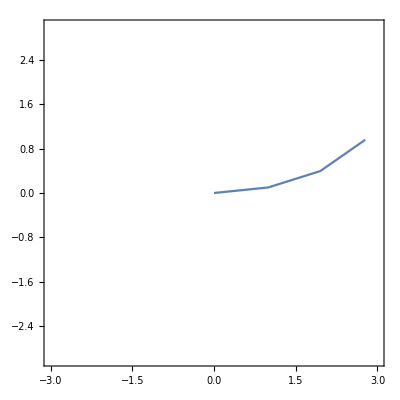

```mathematica
(*Draw a robot arm*)
ListPlot[{p[[1,1;;2]], p[[2,1;;2]], p[[3,1;;2]], p[[4,1;;2]]},
Joined->True,
PlotRange->{{-3,3},{-3,3}},
Frame->True,
AspectRatio->1]
```

```mathematica
(*Give an interface*)
Manipulate[
(*Give an angle set from the interface*)
q={q1,q2,q3};
(*Calculate forward kinematics*)
p = FK[q];
(*Draw a robot arm *)
ListPlot[{p[[1,1;;2]], p[[2,1;;2]], p[[3,1;;2]], p[[4,1;;2]]},
Joined->True,
PlotRange->{{-3,3},{-3,3}},
Frame->True,
AspectRatio->1],
{{q1,0},-π,π},{{q2,0},-π,π},{{q3,0},-π,π}
]
```